# Лабораторная работа №2

Выполнила студентка ММФ БГУ 
КМ, 1 к, 5 гр. Бельская Е.А.
    9 сентября 2019

## 2. Поиск описания Гамма - функции в системе справки

### a)

Help -> Wolfram Documentation -> Symbolic and Numeric Computation -> Mathematical Functions -> Special Functions -> Gamma

### b)

```mathematica
Gamma
```

### c)

```mathematica
?Gamma
```

Gamma[z] is the Euler gamma function Γ(z). 
Gamma[a,z] is the incomplete gamma function Γ(a,z). 
Gamma[a,z_0,z_1] is the generalized incomplete gamma function Γ(a,z_0)-Γ(a,z_1).

## 3. График Гамма - функции

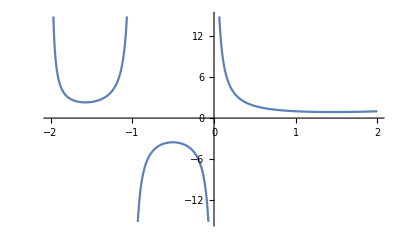

```mathematica
Plot[Gamma[x],{x,-2,2}]
```

## 4. Гамма - функция от натурального аргумента

```mathematica
Gamma/@{ 1,2,3,4,5,6,7}
```

{1,1,2,6,24,120,720}

Если указан один аргумент (i max), то функция Range генерирует лист значений от 1 до i max
Если указаны два аргумента (imin, i max), то функция  Range генерирует лист значений от imin до i max
Если указаны три аргумента (imin, i max, d), то функция  Range генерирует лист значений от imin до i max с шагом d

```mathematica
Gamma/@Range[7]
```

{1,1,2,6,24,120,720}

Вывод : порядок вычисления: считает Gamma для каждого элемента из списка Range

Ответ : значение Гаммы - функции с натуральным аргументом совпадает со значением функции факториал

## 5. Сравнение значений функций Гамма и Факториал

```mathematica
Factorial/@Range[7]
```

{1,2,6,24,120,720,5040}

```mathematica
Γ(n)=(n+1)!
```

Set::write: Tag Times in n Γ is Protected.

(1+n)!

```mathematica
Gamma[#+1]-Factorial[#]&/@Range[15]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Вывод : значения данных функций совпадает при аргументах n для Gamma и (n + 1) для Factorial, поэтому при вычитании в выражении (2) получаются 0 (считает Gamma[n + 1] и Factorial[n]  для каждого элемента из списка Range

## 6. График функции Факториал

### a)

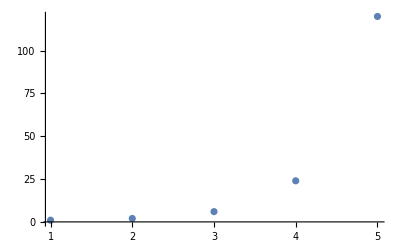

```mathematica
ListPlot[{#, #!}&/@Range[5]]
```

### b)

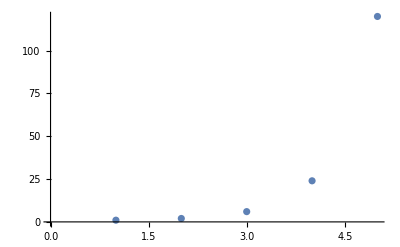

```mathematica
ListPlot[Table[n!,{n,1,5}]]
```

Table[expr, iterator]. Она реализует конструкцию повторения, вычисляет выражение expr при каждом значении локальной переменной i. Множество значений, которые принимает локальная переменная i, описывает аргумент iterator.

## 7. Сравнение поведения Гамма, степенной и показательной функций

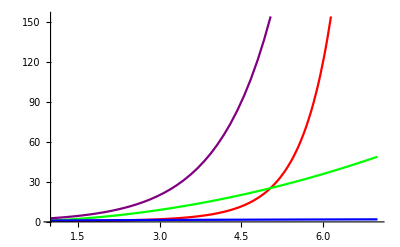

```mathematica
Plot[{Gamma[x], x^2, CubeRoot[x], E^x},{x,1,7}, PlotStyle->{Red, Green, Blue, Purple}]
```

Удобно взять данный промежуток, так как можно определить поведение каждой из предложенных функций

Cо скоростью роста которой функции
можно сопоставить скорость роста Гамма-функции:с функцией экспоненты

## 8. Скорости роста функций

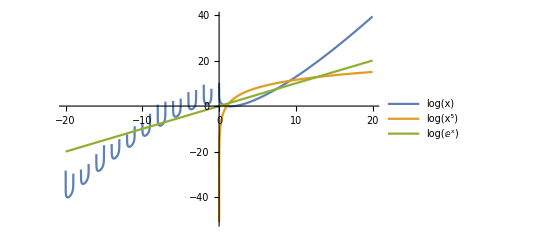

```mathematica
Plot[{Log[Gamma[x]], Log[x^5], Log[E^x]}, {x,-20,20}, PlotLegends->"Expressions"]
```

При x > 0 функция гамма непрепывна, при х < 0 - дискретна. При изменение показателя в показательной функции поведение функции не меняется.

## 9. Рекуррентная формула для Гамма - функции

```mathematica
Plot[(E^(x+1))/(E^x), {x,-1,1}]
```

-Graphics-

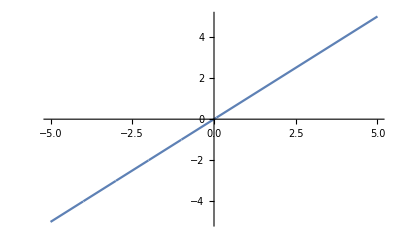

```mathematica
Plot[Gamma[x+1]/Gamma[x], {x,-5,5}]
```

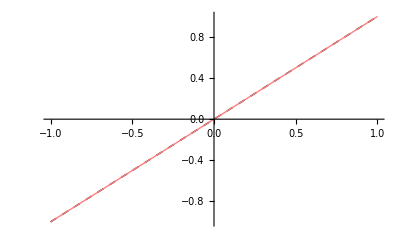

```mathematica
Plot[{x,Gamma[x+1]/Gamma[x]},{x,-1,1}, PlotStyle->{{Thick,Black , Dashed},{Thick,Pink}}]
```

```mathematica
Γ (x+1)=Γ x x
```

Вывод: Таким образом график y= Gamma[x+1]/Gamma[x] совпадает с графиком y=x, значит, Γ (x+1)=x*Γ (x)

## 10. Свойство экспоненты и наша креативность

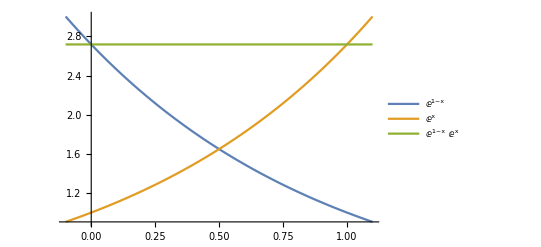

```mathematica
Plot[{E^(1-x), E^x, (E^(1-x))*E^x}, {x, -0.1, 1.1}, PlotLegends->"Expressions"]
```

ⅇ^(1-x) симметрична ⅇ^x относительно какой-то точки с абсциссой 0.5

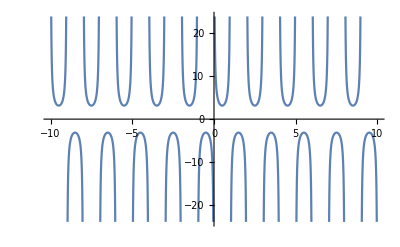

```mathematica
Plot[Gamma[1-x]*Gamma[x], {x, -10,10}]
```

Данная функция периодична

## 11. Наша креативность и гармонические колебания

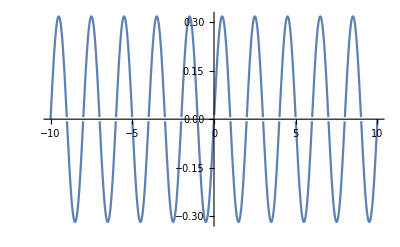

```mathematica
Plot[{1/(Gamma[1-x]*Gamma[x])}, {x, -10,10}]
```

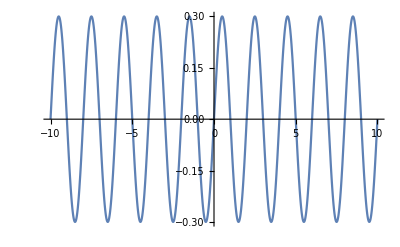

```mathematica
Plot[{0.3*Sin[x*π]}, {x, -10,10}]
```

0.3 sin(π x)=1/(1-x x)

## 12. Основные выводы

```mathematica
Γ n=(n+1)!
```

```mathematica
Γ (x+1)=Γ x x
```